```mathematica
n=7
N[1/Factorial[1+n]*(n+2)/(n+1)]
```

7

0.0000279018

```mathematica
Sum[1/n!,{n,0,7}]
```

685/252

```mathematica
N[%]
```

2.71825

```mathematica
Log[500]
```

Log[500]

```mathematica
N[%]
```

6.21461

```mathematica
m=2
N[(12/(8^3))^m*96/(8^3-12)]
```

2

0.000105469

```mathematica
2
```

2

```mathematica
N[8*(1-1/3*12/8^3-1/3*2/3/2*(12/8^3)^2)]
```

7.93701

```mathematica
N[CubeRoot[500]]
```

7.93701

```mathematica
1/2-1/10/32+1/24/512-5/16/13/8192
```

12701653/25559040

```mathematica
N[%]
```

0.496953

```mathematica
N[Integrate[1/Sqrt[1+x^4],{x,0,1/2}]]
```

0.496954+2.77556×10^-17 ⅈ

```mathematica
5/16/13/8192
```

5/1703936

```mathematica
N[%]
```

2.93438×10^-6

```mathematica
1/48/7/4^7
```

1/5505024

```mathematica
N[%]
```

1.81652×10^-7

```mathematica
2NProduct[(1/12-n)/(n+1)*(-96/4096),{n,0,1}]*4096^2/4000^2
```

-0.000044

```mathematica
2-2/12*96/4096
```

511/256

```mathematica
N[%]
```

1.99609

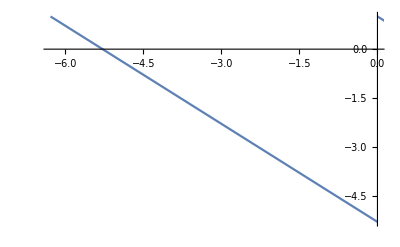

```mathematica
g1=Plot[{-(x+2*Pi)+1},{x,-2*Pi,0}];
g2=Plot[{-x+1},{x,0,2*Pi}];
g3=Plot[{-(x-2*Pi)+1},{x,2*Pi,4*Pi}];
Show[g1,g2,g3,Range->Full]
```


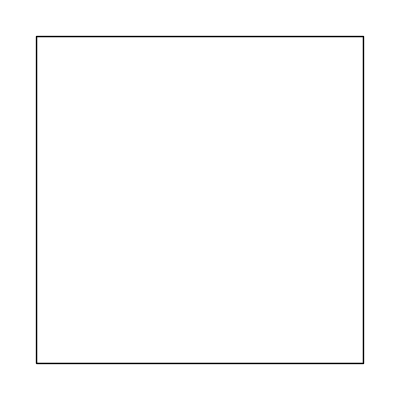

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{m1,m2,m3,m4}=Graphics/@{{EdgeForm[Thick],White,Disk[{0,0},1]},Disk[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]}
```

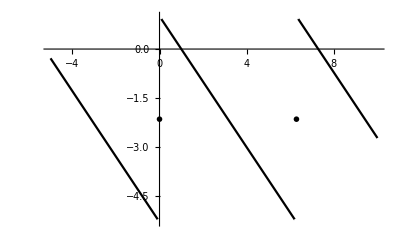

```mathematica
Show[Plot[Piecewise[{{-(x+2*Pi)+1,x<0&&x>-2*Pi},{-x+1,x>0&&x<2*Pi},{-(x-2*Pi)+1,x>2*Pi&&x<4*Pi}}],{x,-5,10},AxesStyle->Arrowheads[0.04],PlotStyle->Black],ListPlot[{{0,1-Pi},{2*Pi,1-Pi}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m2,0.04}],ListPlot[{{0,1},{0,1-2*Pi},{2*Pi,1},{2*Pi,1-2*Pi}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m1,0.04}]]
```

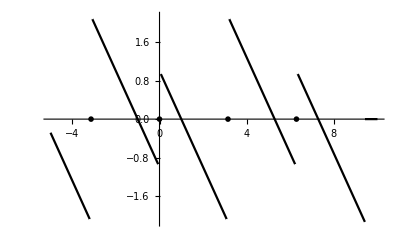

```mathematica
Show[Plot[Piecewise[{{-(x+2*Pi)+1,x<-Pi&&x>-2*Pi},{-x-1,x<0&&x>-Pi},{-x+1,x>0&&x<Pi},{-(x-2*Pi)-1,x>Pi&&x<2*Pi},{-(x-2*Pi)+1,x>2*Pi&&x<3*Pi}}],{x,-5,10},AxesStyle->Arrowheads[0.04],PlotStyle->Black],ListPlot[{{-Pi,0},{0,0},{Pi,0},{2*Pi,0}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m2,0.04}],ListPlot[{{-Pi,1-Pi},{-Pi,Pi-1},{0,1},{0,-1},{Pi,1-Pi},{Pi,Pi-1},{2*Pi,1},{2*Pi,-1}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m1,0.04}]]
```

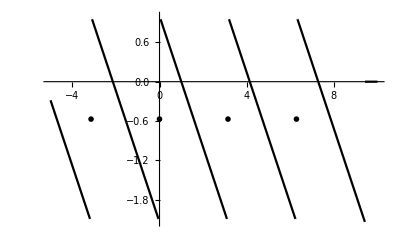

```mathematica
Show[Plot[Piecewise[{{-(x+2*Pi)+1,x<-Pi&&x>-2*Pi},{-(x+Pi)+1,x<0&&x>-Pi},{-x+1,x>0&&x<Pi},{-(x-Pi)+1,x>Pi&&x<2*Pi},{-(x-2*Pi)+1,x>2*Pi&&x<3*Pi}}],{x,-5,10},AxesStyle->Arrowheads[0.04],PlotStyle->Black],ListPlot[{{-Pi,1-Pi/2},{0,1-Pi/2},{Pi,1-Pi/2},{2*Pi,1-Pi/2}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m2,0.04}],ListPlot[{{-Pi,1-Pi},{-Pi,1},{0,1},{0,1-Pi},{Pi,1-Pi},{Pi,1},{2*Pi,1},{2*Pi,1-Pi}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m1,0.04}]]
```

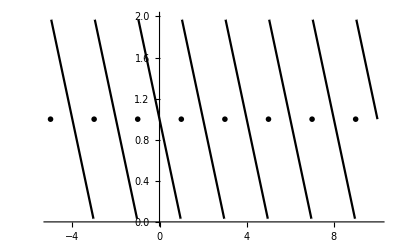

```mathematica
Show[Plot[Piecewise[{{-(x+4)+1,x>-5&&x<-3},{-(x+2)+1,x>-3&&x<-1},{-x+1,x>-1&&x<1},{-(x-2)+1,x>1&&x<3},{-(x-4)+1,x>3&&x<5},{-(x-6)+1,x>5&&x<7},{-(x-8)+1,x>7&&x<9},{-(x-10)+1,x>9&&x<11}}],{x,-5,10},AxesStyle->Arrowheads[0.04],PlotStyle->Black],ListPlot[{{-5,1},{-3,1},{-1,1},{1,1},{3,1},{5,1},{7,1},{9,1}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m2,0.04}],ListPlot[{{-5,2},{-3,0},{-3,2},{-1,0},{-1,2},{1,0},{1,2},{3,0},{3,2},{5,0},{5,2},{7,0},{7,2},{9,0},{9,2}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m1,0.04}]]
```